```mathematica
M0=40;e=2;b0=60;
```

```mathematica
G=6.67408 10^-11;MS=1.898 10^30;M=M0 MS;c=3 10^8;Mpc=10^6 3.086 10^16;inc=Pi/3;η=1/4;d=1 Mpc;b=b0 (G M)/c^2;ti=0.4;
```

```mathematica
hx=-2 (-2 cos2ϕ dr rdphi+sin2ϕ (-dr^2+rdphi^2+z)) Cos[inc];
```

```mathematica
hp=-((2 dr rdphi sin2ϕ+cos2ϕ (-dr^2+rdphi^2+z)) (1+Cos[inc]^2)+(-dr^2-rdphi^2+z) Sin[inc]^2);
```

```mathematica
U=u1/.FindRoot[#2 Sinh[u1]-u1==#1,{u1,0}]&;
```

```mathematica
uarr={};
```

```mathematica
nbref=nb/.y->1/c^2/.et->e/.b0->60
```

27.9496

```mathematica
mx=ti;pts=100;
```

```mathematica
tarr=Table[l//N,{l,-mx,mx,2 mx/(pts-1)}];
```

```mathematica
larr=nbref tarr;
```

```mathematica
uarr={};
```

```mathematica
Do[AppendTo[uarr,U[larr[[i]],e]],{i,1,pts}]
```

```mathematica
uarr;
```

```mathematica
rep={y->1/c^2,cos2ϕ->Cos[2 phib],dr->rtb,rdphi->rphitb,sin2ϕ->Sin[2 phib],dr->rtb,z->zb,v->vb,eϕ->ephietb et,et->e};
```

```mathematica
sc=(G M η)/(c^4 d);
```

```mathematica
hparr={};
```

```mathematica
Do[AppendTo[hparr,hp sc//.rep/.u->uarr[[i]]],{i,1,pts}]
```

```mathematica
hxarr={};
```

```mathematica
Do[AppendTo[hxarr,hx sc//.rep/.u->uarr[[i]]],{i,1,pts}]
```

```mathematica
hpplot={};Do[AppendTo[hpplot,{tarr[[i]],hparr[[i]]-hparr[[1]]}],{i,1,pts}]
```

```mathematica
hxplot={};Do[AppendTo[hxplot,{tarr[[i]],hxarr[[i]]-hxarr[[1]]}],{i,1,pts}]
```

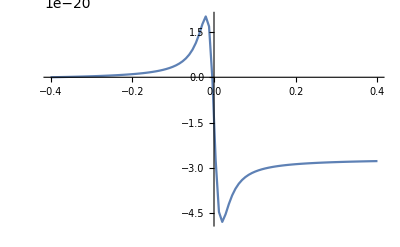

```mathematica
plot=ListLinePlot[hxplot,PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/subhajit/Dropbox/LIGO/Original/sample_LAL/tosend

```mathematica
Export["M_"<>ToString[M0]<>"e_"<>ToString[e]<>"b_"<>ToString[b0]<>".png",plot]
```

M_40e_2b_60.png